## recursive calculation of the likelihood in gaussian markov trees (BAR model)

theory

#### The process is defined by p(x_1,x_2|x) =(det(2π C_12))^(-1/2)ⅇ^(-1/2{[(x_1 x_2)-A_12 x]ᵀ C_12^-1[(x_1 x_2)-A_12 x]}) . Here A_12 is the deterministic regression to the mean for both daughters, x_i are the d-dimensional hidden variables for the daughters, and C_12 is the conditioned daughter covariance, which is x-independent.

#### Using this basic relation, and the linear map τ=α·x (transformation of τ including log and shift is done afterwards) for the observed time, we want to calculate the likelihood p(τ^<|x). Here τ^< is the vector of all cycle times of descendants of the mother cell with the hidden state x. I.e. the higher up in the tree, the bigger τ^< (exponentially).

#### This probability has the Gaussian form p(τ^<|x)=(Z^<)^-1 ⅇ^(-1/2{(τ^<-μ_τ^<)ᵀ(C^<)^-1(τ^<-μ_τ^<)}), where the mean μ_τ^<=M^<x+c^< is an affine function of x.

#### It turns out that in fact c^<=0 always, and that the covariance is independent of x.

#### In each recursive update step, going from the two daughters to the mother, the data M^<, C^< have to be updated from their values M_i^<, C_i^< for each of the daughters.

#### To effect this update, we write p(τ^<|x)=p(τ_1,τ_2,τ_1^<,τ_2^<|x)=∫p(x_1,x_2|x)∏_i δ(τ_i-α·x_i)p(τ_i^<|x_i)ⅆ x_i. where τ_i^< are the descendants of each daughter. In this expression, note that the probability of all times downstream of x_i depends on x_i but not on x. This is a consequence of the Markov inheritance of x. Likewise the probability of x_i depends only on x not further upstream cells.

#### The task is to derive the recursive update rule for M^<, C^< from the probability relation in the basic update formula above.

## The calculation for x_12

#### Instead of immediately calculating p(τ_1,τ_2,τ_1^<,τ_2^<|x), we postpone the projection on the times and first calculate p=p(x_1,x_2,τ_1^<,τ_2^<|x) =p(x_1,x_2|x)p(τ_1^<|x_1)p(τ_2^<|x_2) =ⅇ^(-1/2{(x_12-A_12 x)ᵀC_12^-1(%) + (τ_12^<-M_12^<x_12)ᵀ(C_12^<)^-1(%)}), where: x_12=(x_1 x_2) is the stacked hidden vector of daughters 1 and 2. A_12=stack(A,A)=(A A) is the stacked inheritance matrix. A_12 x has to make sense dimension wise: A_12 is 2d×d. M_12^<=diag(M_1^<,M_2^<) is block diagonal and has dimension (#_(1<)+#_(2<))×2d where the # indicate the number of children. C_12^(<-1)=diag(C_1^(<-1),C_2^(<-1)) is constructed from the recursive mean and covariance matrices for each branch. it has dims (#_(1<)+#_(2<))^2. Note that the stiffnesses (inverse stiffnesses) are composed in block diagonal form, not the covariances.

#### We now need to collect the terms in this pdf to write it as a pdf for x_12 and τ_12^<. We start by expanding in block form

#### p∝ⅇ^(-1/2(x x_12 τ_12^<)ᵀS_3(x x_12 τ_12^<))=ⅇ^(-1/2{(x x_12 τ_12^<)ᵀ(A_12 ᵀ C_12^-1 A_12 | -A_12 ᵀ C_12^-1 | 0 % | ((Ĉ)_12)^-1 | -M_12^<ᵀ(C_12^<)^-1 0 | % | (C_12^<)^-1)(%)}) where ((Ĉ)_12)^-1=C_12^-1+M_12^<ᵀ(C_12^<)^-1 M_12^<.

#### In the expression ((Ĉ)_12)^-1, the blocks 1 and 2 are still uncoupled, since C_12^-1, M_12^< and (C_12^<)^-1 are all block diagonal.

#### We collect the first and second powers of x_12 and τ_12^<. We use the general form (for a symmetric block matrix): (y x)ᵀ(C | Dᵀ D | A)(y x)=(x+A^-1 D y)ᵀA(%)+yᵀ(C-Dᵀ A^-1 D)(%) (*); where (%) indicates repetition of the vector to get a quadratic form.

#### Also, consider the general block inverse relations (α_11 | α_12 α_21 | α_22)^-1=(β_11 | β_12 β_21 | β_22) where β_11=(α_11-α_12 α_22^-1 α_21)^-1=α_11^-1+α_11^-1 α_12 β_22 α_21 α_11^-1, β_21=-α_22^-1 α_21 β_11 (and β_12,β_22 follow by swapping 1 and 2).

#### To calculate p, we need the inverse of the lower right 2x2 block of the 3x3 block matrix S_3 in the exponent, which we call α (and the inverse, β). We also let D denote the lower left 2x1 block.

#### One obtains β_11=C_12^(+1), β_21=M_12^<C_12 so that α^-1 D=β D = (β_11 D_1+β_21 D_2 β_21 D_1+β_21 D_2)=(-A_12 -M_12^<A_12) (note D_2=0) and Dᵀβ D=+A_12 ᵀ C_12^-1 A_12.

#### Result: the yy correction term in (*) cancels, and we are left with

#### p∝ⅇ^(-1/2{[(x_12 τ_12^<)-M_x^<x]ᵀ(C_x^<)^-1[(x_12 τ_12^<)-M_x^<x]}) where M_x^<=(I M_12^<)A_12 and (C_x^<)^-1=(((Ĉ)_12)^-1 | -M_12^<ᵀ(C_12^<)^-1 % | (C_12^<)^-1).

## The projection on the times

#### Now we need to integrate to get the density also for τ_12. we introduce the matrix P_12=||α(||)^-1(α | 0 0 | α) and a matrix Q_12 so that the concatenated columns [P_12 Q_12] form an orthogonal matrix. P_12 ᵀ P_12 and Q_12 ᵀ Q_12 are orthogonal projections. we abbreviate P=P_12 and equivalently for Q. We also define O=diag([P Q],I) where I is an identity matrix.

#### Now, p=p(τ_12,τ_12^<|x)∝∫d x_12 δ^2(τ_12-||α||Pᵀ x_12)ⅇ^(-1/2{(Pᵀ(x_12-A_12 x) Qᵀ(x_12-A_12 x) τ_12^<-M_12^<A_12 x)ᵀOᵀ(C_x^<)^-1 O(%)}). After integrating the parallel directions picked up by P we get a remaining integral over the transversal directions. p∝∫d (Qᵀ x_12)ⅇ^(-1/2{(||α(||)^-1 τ_12-Pᵀ A_12 x Qᵀ(x_12-A_12 x) τ_12^<-M_12^<A_12 x)ᵀOᵀ(C_x^<)^-1 O(%)}) where Oᵀ(C_x^<)^-1 O=([P Q]ᵀ((Ĉ)_12)^-1[P Q] | -[P Q]ᵀM_12^<ᵀ(C_12^<)^-1 % | (C_12^<)^-1)≡Γ.

#### To integrate over the transversal directions we have to invert Γ, erase the transversal blocks, and invert back. Let Γ^-1=Δ then, by the block inversion, Δ_11=(Γ_11-Γ_12 Γ_22^-1 Γ_21)^-1=[P Q]ᵀC_12[P Q], Δ_21=+M_12^<C_12[P Q] Δ_22=C_12^<+M_12^<C_12 M_12^<ᵀ.

#### The reduced covariance Δ becomes then only the P part of this, namely Δ'=(Pᵀ C_12 P | Pᵀ C_12 M_12^<ᵀ % | C_12^<+M_12^<C_12 M_12^<ᵀ)

#### To get the final stiffness matrix we need to invert Δ' to obtain the result Γ'. The lower right block is big, so we want to avoid inverting that directly in a recursive update. Note that in the recursion, we already have from previous recursive steps (C_12^<)^-1=diag((C_1^<)^-1,(C_2^<)^-1). Therefore we use the Sherman–Morrison identity (A+U V)^-1=A^-1-A^-1 U(I+V A^-1 U)V A^-1 with A=C_12^<, U=M_12^<, Vᵀ=M_12^<C_12. This gives (Δ'_22)^-1=(C_12^<)^-1-(C_12^<)^-1(M_12^<[C_12^-1+M_12^<ᵀ(C_12^<)^-1 M_12^<])^-1 M_12^<ᵀ(C_12^<)^-1. In this formula, the inverse of the bracket is of small dimension, and the other inverses are known.

#### We can then complete the block inversion of Δ': (Γ')_11 = (Pᵀ(C_12-C_12 M_12^<ᵀ((Δ')_22)^-1 M_12^<C_12)P)^-1, (Γ')_21=-((Δ')_22)^-1 M_12^<C_12(P(Γ'))_11, (Γ')_22=((Δ')_22)^-1+((Δ')_22)^-1 M_12^<C_12(P(Γ'))_11 Pᵀ C_12 M_12^<ᵀ((Δ')_22)^-1 = ((Δ')_22)^-1+(Γ')_21((Γ')_11)^-1(Γ')_12

## Determinant update

#### If required for performance, we can try to update the determinant with the block matrix formula det (A | B C | D)=det A det (D-C A^-1 B). This could avoid determinants of growing size. In the current implementation, this turns out not to be a bottleneck, so it is not done.

## The final result

#### the final result becomes: p(τ^<|x)=p(τ_12,τ_12^<|x) ∝ⅇ^(-1/2{[(τ_12 τ_12^<)-(||α||Pᵀ A_12 x M_12^<x)]ᵀ(||α(||)^-1 | 0 0 | I)Γ'(||α(||)^-1 | 0 0 | I)[%]}) =ⅇ^(-1/2{[τ^<-M^<x]ᵀ(C^<)^-1[%]}), where M^<=(||α||Pᵀ M_12^<)A_12 and C^<=(||α(||)^-1 | 0 0 | I)Γ'(||α(||)^-1 | 0 0 | I), with Γ' as above.

now a Mathematica prototype of this recursive likelihood:

### utilities

```mathematica
P12[α_]:=Module[{a={α}ᵀ/Norm[α]},ArrayFlatten@({{a, 0}, {0, a}})]
```

```mathematica
P1[α_]:={α}ᵀ/Norm[α]
```

```mathematica
P12[{3.,4.,.53}]//Chop//MatrixForm
```

(0.596657 | 0
0.795543 | 0
0.105409 | 0
0 | 0.596657
0 | 0.795543
0 | 0.105409)

```mathematica
stackdiag[m1_,{{}}]:=m1
stackdiag[{{}},m2_]:=m2
stackdiag[m1_,m2_]:=ArrayFlatten@({{m1, 0}, {0, m2}})
```

```mathematica
stackhigh[m1_,{{}}]:=m1
stackhigh[{{}},m2_]:=m2
stackhigh[m1_,m2_]:=ArrayFlatten@({{m1}, {m2}})
```

```mathematica
zerosLike[m_]:=ConstantArray[0,Dimensions@m]
```

```mathematica
zeroFilled[{ML1_,ML2_,CIL1_,CIL2_}]:=Which[
ML2=={{}},
{ML1,zerosLike@ML1,CIL1,zerosLike@CIL1,Range@Length@ML1},
ML1=={{}},
{zerosLike@ML2,ML2,zerosLike@CIL2,CIL2,Range[Length@ML2+1,2Length@ML2]},
True,
{ML1,ML2,CIL1,CIL2,Range[Length@ML1+Length@ML2]}]
```

```mathematica
stiffness1[stiffness12_]:=Module[{d},
d=Length[stiffness12]/2;
Inverse[Inverse[stiffness12][[;;d,;;d]] ] ]
```

```mathematica
pp[M_][MM_]:=M.MM.Mᵀ
```

### as before, notation convention : C = C covariance matrix, CI = inverse covariance, L = “<” superscript, H = hat, 12 = 12 subscripts.

### In each recursive step, we wish to update ML, CIL from their values on the branches.

### The update of ML is easier. Do it first.

#### case: two branches, at least one with descendants

```mathematica
ML[A_,α_,CI12_][ {ML1_, CIL1_}, {ML2_, CIL2_}]:=
Module[{P,a12,nα,ml12,ml1, ml2, cil1, cil2, drange},
P=P12[α];
nα=Norm@α;
a12=stackhigh[A,A];
(*Print[Dimensions/@{ML1,ML2}];*)
{ml1,ml2,cil1,cil2,drange}=zeroFilled[{ML1,ML2,CIL1,CIL2}];
ml12=stackdiag[ml1,ml2];
(*Print[Dimensions[ml12]];*)
stackhigh[nα * Pᵀ,ml12[[drange,;;]]].a12
]
```

#### case: two children which are leaves

```mathematica
ML[A_,α_,CI12_][ {{{}},{{}}},{{{}},{{}}}]:=
Module[{ch12,a12,nα},
a12=stackhigh[A,A];
nα=Norm@α;
nα*P12[α]ᵀ.a12
]
```

#### case: one child which is a leaf

```mathematica
ML[A_,α_,CI12_][ {{{}},{{}}}]:=
Module[{P,nα},
nα=Norm@α;
P=P1[α];
nα* Pᵀ.A
]
```

#### case : one child with descendants

```mathematica
ML[A_,α_,CI12_][ {ML1_, CIL1_}]:=
Module[{P,nα},
nα=Norm@α;
P=P1[α];
stackhigh[nα * Pᵀ,ML1].A
]
```

### Now the update of CIL.

#### First do the case with two children with descendants

#### First we need (Δ'_22)^-1=(C_12^<)^-1-(C_12^<)^-1(M_12^<(C_12^-1+M_12^<ᵀ(C_12^<)^-1 M_12^<))^-1 M_12^<ᵀ(C_12^<)^-1

```mathematica
DeltaPI22[A_,α_,CI12_][ {ML1_, CIL1_}, {ML2_, CIL2_}]:=
Module[{ml12, ml1, ml2, cil1, cil2, drange,cil12,pi,dl},
{ml1,ml2,cil1,cil2,drange}=zeroFilled[{ML1,ML2,CIL1,CIL2}];
ml12=stackdiag[ml1,ml2];
cil12=stackdiag[cil1,cil2];
pi=Inverse[CI12+pp[ml12ᵀ][cil12]];(*small*)
dl=cil12-pp[cil12.ml12][pi];
(*dl[[drange,drange]];*)
dl
]
```

#### Now we can do the block inverse for Γ' using (Γ')_11 = (Pᵀ(C_12-C_12 M_12^<ᵀ((Δ')_22)^-1 M_12^<C_12)P)^-1, (Γ')_21=-((Δ')_22)^-1 M_12^<C_12(P(Γ'))_11, (Γ')_22=((Δ')_22)^-1+((Δ')_22)^-1 M_12^<C_12(P(Γ'))_11 Pᵀ C_12 M_12^<ᵀ((Δ')_22)^-1

```mathematica
GammaP[A_,α_,CI12_][ {ML1_, CIL1_}, {ML2_, CIL2_}]:=
Module[{ml12, ml1, ml2, cil1, cil2, drange,cil12,pi,DPI22,g11,g21,g22,g12,P,c12},
c12=Inverse[CI12];(*small, ok.*)
P=P12[α];
{ml1,ml2,cil1,cil2,drange}=zeroFilled[{ML1,ML2,CIL1,CIL2}];
ml12=stackdiag[ml1,ml2];
cil12=stackdiag[cil1,cil2];
DPI22=DeltaPI22[A,α,CI12][{ML1,CIL1},{ML2,CIL2}];
Print[{c12, ml12,DPI22}];
g11=Inverse[pp[Pᵀ][c12-pp[c12.ml12ᵀ][DPI22]]];
g21=-DPI22.ml12.c12.P.g11;
g12=g21ᵀ;
g22=DPI22+pp[DPI22.ml12.c12.P][g11];
ArrayFlatten@({{g11, g12[[;;,drange]]}, {g21[[drange,;;]], g22[[drange,drange]]}})
]
```

#### and get the result

```mathematica
CIL[A_,α_,CI12_][ {ML1_, CIL1_}, {ML2_, CIL2_}]:=
Module[{gp,ascale,d},
gp=GammaP[A,α,CI12][ {ML1, CIL1}, {ML2, CIL2}];
d=Length@gp-2;
ascale=ArrayFlatten@({{1/Norm[α]*IdentityMatrix@2, 0}, {0, IdentityMatrix@d}});
pp[ascale][gp]
]
```

#### Now the case with two leaf children.

```mathematica
GammaP[A_,α_,CI12_][{{{}},{{}}},{{{}},{{}}}]:=
Module[{g11,P,c12},
c12=Inverse[CI12];(*small, ok.*)
P=P12[α];
g11=Inverse[pp[Pᵀ][c12]];
g11
]
```

```mathematica
CIL[A_,α_,CI12_][ {{{}},{{}}},{{{}},{{}}}]:=
Module[{gp},
gp=GammaP[A,α,CI12][ {{{}},{{}}},{{{}},{{}}}];
pp[1/Norm[α]IdentityMatrix@2][gp]
]
```

#### Case: one child which is a leaf

```mathematica
GammaP[A_,α_,CI12_][ {{{}},{{}}}]:=
Module[{g11,P,c1},
c1=Inverse[stiffness1[CI12]];(*small, ok.*)
P=P1[α];
g11=Inverse[pp[Pᵀ][c1]];
g11
]
```

```mathematica
CIL[A_,α_,CI12_][  {{{}},{{}}}]:=Module[{gp},
gp=GammaP[A,α,CI12][{{{}},{{}}}];
pp[1/Norm[α]IdentityMatrix@1][gp]
]
```

#### Case: one child with descendants

```mathematica
DeltaPI22[A_,α_,CI12_][ {ML1_, CIL1_}]:=
Module[{pi,ci1},
ci1=stiffness1[CI12];
pi=Inverse[ci1+pp[ML1ᵀ][CIL1]];(*small*)
CIL1-pp[CIL1.ML1][pi]
]
```

```mathematica
GammaP[A_,α_,CI12_][ {ML1_, CIL1_}]:=
Module[{pi,DPI22,g11,g21,g22,g12,P,c1,ci1},
ci1=stiffness1[CI12];
c1=Inverse[ci1];(*small*)
P=P1[α];
DPI22=DeltaPI22[A,α,CI12][{ML1,CIL1}];
g11=Inverse[pp[Pᵀ][c1-pp[c1.ML1ᵀ][DPI22]]];
g21=-DPI22.ML1.c1.P.g11;
g12=g21ᵀ;
g22=DPI22+pp[DPI22.ML1.c1.P][g11];
ArrayFlatten@({{g11, g12}, {g21, g22}})
]
```

```mathematica
CIL[A_,α_,CI12_][ {ML1_, CIL1_}]:=
Module[{gp,ascale,d},
gp=GammaP[A,α,CI12][ {ML1, CIL1}];
d=Length@gp-1;
ascale=ArrayFlatten@({{1/Norm[α]IdentityMatrix@1, 0}, {0, IdentityMatrix@d}});
pp[ascale][gp]
]
```

### Now, we can plug these together in a recursion rule.

## Tests of the recursive definition

#### parameters. make sure α is not EV of A or Aᵀ.

```mathematica
I2=IdentityMatrix@2;
A=({{.5, .2}, {0, .4}});
α={.1,.1};
CI12=Inverse@ArrayFlatten@({{I2, .3I2}, {.3I2, I2}})
```

{{1.0989,0.,-0.32967,0.},{0.,1.0989,0.,-0.32967},{-0.32967,0.,1.0989,0.},{0.,-0.32967,0.,1.0989}}

```mathematica
Eigenvectors[Aᵀ]
```

{{0.447214,0.894427},{0.,1.}}

```mathematica
α.A
```

{0.05,0.06}

#### initial conditions. two leaf children:

```mathematica
ML[A,α,CI12][{{{}},{{}}},{{{}},{{}}}]
```

{{0.05,0.06},{0.05,0.06}}

```mathematica
MLstart={α.A,α.A}
```

{{0.05,0.06},{0.05,0.06}}

```mathematica
CILstart=Inverse[P12[α]ᵀ.Inverse[CI12].P12[α]]/α.α
```

{{54.9451,-16.4835},{-16.4835,54.9451}}

```mathematica
CIL[A,α,CI12][{{{}},{{}}},{{{}},{{}}}]
```

{{54.9451,-16.4835},{-16.4835,54.9451}}

```mathematica
CIL[A,α,CI12][{{{}},{{}}}]
```

{{50.}}

```mathematica
(#//Inverse//MatrixForm)&/@{%,%%}
```

{(0.02),(0.02 | 0.006
0.006 | 0.02)}

### same covariance for 1 or 2 leaf children. good.

```mathematica
P12[α]
```

{{0.707107,0},{0.707107,0},{0,0.707107},{0,0.707107}}

#### two children, each with MLstart, CILstart, i.e. with two leaf children each.

```mathematica
(#[A,α,CI12][ {MLstart,CILstart},{MLstart,CILstart}]//Chop)&/@{ML,CIL}//MatrixForm/@#&
```

{{{1.,0.,0.3,0.},{0.,1.,0.,0.3},{0.3,0.,1.,0.},{0.,0.3,0.,1.}},{{0.05,0.06,0,0},{0.05,0.06,0,0},{0,0,0.05,0.06},{0,0,0.05,0.06}},{{48.9246,-22.504,-1.2657,-1.2657},{-22.504,48.9246,-1.2657,-1.2657},{-1.2657,-1.2657,48.9246,-22.504},{-1.2657,-1.2657,-22.504,48.9246}}}

{(0.05 | 0.06
0.05 | 0.06
0.025 | 0.034
0.025 | 0.034
0.025 | 0.034
0.025 | 0.034),(78.1252 | -16.5102 | -21.0728 | -21.0728 | 0.0242216 | 0.0242216
-16.5102 | 78.1252 | 0.0242216 | 0.0242216 | -21.0728 | -21.0728
-21.0728 | 0.0242216 | 54.8714 | -16.5572 | -0.0220197 | -0.0220197
-21.0728 | 0.0242216 | -16.5572 | 54.8714 | -0.0220197 | -0.0220197
0.0242216 | -21.0728 | -0.0220197 | -0.0220197 | 54.8714 | -16.5572
0.0242216 | -21.0728 | -0.0220197 | -0.0220197 | -16.5572 | 54.8714)}

#### the stiffness matrix contains empty blocks in the special case that α is an eigenvector of Aᵀ. Namely, no coupling of aunts and nieces.

#### the covariances do not uncouple :

```mathematica
Inverse[CIL[A,α,CI12][ {MLstart,CILstart},{MLstart,CILstart}]]//MatrixForm
```

{{{1.,0.,0.3,0.},{0.,1.,0.,0.3},{0.3,0.,1.,0.},{0.,0.3,0.,1.}},{{0.05,0.06,0,0},{0.05,0.06,0,0},{0,0,0.05,0.06},{0,0,0.05,0.06}},{{48.9246,-22.504,-1.2657,-1.2657},{-22.504,48.9246,-1.2657,-1.2657},{-1.2657,-1.2657,48.9246,-22.504},{-1.2657,-1.2657,-22.504,48.9246}}}

(0.02 | 0.006 | 0.011 | 0.011 | 0.0033 | 0.0033
0.006 | 0.02 | 0.0033 | 0.0033 | 0.011 | 0.011
0.011 | 0.0033 | 0.0261 | 0.0121 | 0.00183 | 0.00183
0.011 | 0.0033 | 0.0121 | 0.0261 | 0.00183 | 0.00183
0.0033 | 0.011 | 0.00183 | 0.00183 | 0.0261 | 0.0121
0.0033 | 0.011 | 0.00183 | 0.00183 | 0.0121 | 0.0261)

#### one non-leaf child with two children, one leaf child.

```mathematica
(#[A,α,CI12][ {MLstart,CILstart},{{{}},{{}}}]//Chop)&/@{ML,CIL}//MatrixForm/@#&
```

{{{1.,0.,0.3,0.},{0.,1.,0.,0.3},{0.3,0.,1.,0.},{0.,0.3,0.,1.}},{{0.05,0.06,0,0},{0.05,0.06,0,0},{0,0,0,0},{0,0,0,0}},{{48.8033,-22.6253,0.,0.},{-22.6253,48.8033,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}}

{(0.05 | 0.06
0.05 | 0.06
0.025 | 0.034
0.025 | 0.034),(78.1251 | -16.4835 | -21.0728 | -21.0728
-16.4835 | 54.9451 | 0 | 0
-21.0728 | 0 | 54.8714 | -16.5572
-21.0728 | 0 | -16.5572 | 54.8714)}

```mathematica
%[[2,1]]//Inverse//MatrixForm
```

(0.02 | 0.006 | 0.011 | 0.011
0.006 | 0.02 | 0.0033 | 0.0033
0.011 | 0.0033 | 0.0261 | 0.0121
0.011 | 0.0033 | 0.0121 | 0.0261)

#### two leaf children

```mathematica
(#[A,α,CI12][ {{{}},{{}}},{{{}},{{}}}]//Chop)&/@{ML,CIL}//MatrixForm/@#&
```

{(0.05 | 0.06
0.05 | 0.06),(54.9451 | -16.4835
-16.4835 | 54.9451)}

```mathematica
%[[2,1]]//Inverse//MatrixForm
```

(0.02 | 0.006
0.006 | 0.02)

#### one nonleaf child

```mathematica
(#[A,α,CI12][ {MLstart,CILstart}]//Chop)&/@{ML,CIL}//MatrixForm/@#&
```

{(0.05 | 0.06
0.025 | 0.034
0.025 | 0.034),(73.1801 | -21.0728 | -21.0728
-21.0728 | 54.8714 | -16.5572
-21.0728 | -16.5572 | 54.8714)}

```mathematica
%[[2,1]]//Inverse//MatrixForm
```

(0.02 | 0.011 | 0.011
0.011 | 0.0261 | 0.0121
0.011 | 0.0121 | 0.0261)

#### one leaf child

```mathematica
(#[A,α,CI12][ {{{}},{{}}}]//Chop)&/@{ML,CIL}//MatrixForm/@#&
```

{(0.05 | 0.06),(50.)}

```mathematica
α.A
```

{0.05,0.06}

#### observation : if α is a left eigenvector of A, then the combined stiffness has all the naively expected block structure.

### The recursive function.

```mathematica
treestruct := {τ,
{}
|{sub_/;MatchQ[sub,treestruct]}
|{sub1_/;MatchQ[sub1,treestruct],sub2_/;MatchQ[sub2,treestruct]}
}
```

```mathematica
Clear@MCIL
```

#### no child. empty case.

```mathematica
MCIL[A_,α_,CI12_][{τ,{}}]:=
{{{}},{{}}}
```

#### one leaf child

MCIL[A_, α_, CI12_][{τ, {down : {τ, {}}}}] :=
 (#[A, α, CI12][ {{{}}, {{}}}] // Chop) & /@ {ML, CIL}

#### one child, leaf or not.

```mathematica
MCIL[A_,α_,CI12_][{τ,{down:treestruct} }]:=
Module[{mcil},
mcil = MCIL[A,α,CI12][down];
(#[A,α,CI12][mcil])&/@{ML,CIL}]
```

#### two children

```mathematica
MCIL[A_,α_,CI12_][{τ,{down1:treestruct, down2:treestruct} }]:=
Module[{mcil1,  mcil2},
{mcil1, mcil2} = MCIL[A,α,CI12]/@{down1,down2};
(#[A,α,CI12][mcil1, mcil2])&/@{ML,CIL}]
```

### now let' s construct a tree structure

```mathematica
fullstruct[1]:={τ,{}}
fullstruct[n_]:={τ,{fullstruct[n-1],fullstruct[n-1]}}
```

```mathematica
chain[1]:={τ,{}}
chain[n_]:={τ,{chain[n-1]}}
```

```mathematica
MatchQ[fullstruct[14],treestruct]
```

True

```mathematica
fullstruct[5]
```

{τ,{{τ,{{τ,{{τ,{{τ,{}},{τ,{}}}},{τ,{{τ,{}},{τ,{}}}}}},{τ,{{τ,{{τ,{}},{τ,{}}}},{τ,{{τ,{}},{τ,{}}}}}}}},{τ,{{τ,{{τ,{{τ,{}},{τ,{}}}},{τ,{{τ,{}},{τ,{}}}}}},{τ,{{τ,{{τ,{}},{τ,{}}}},{τ,{{τ,{}},{τ,{}}}}}}}}}}

```mathematica
%//TreeForm;
```

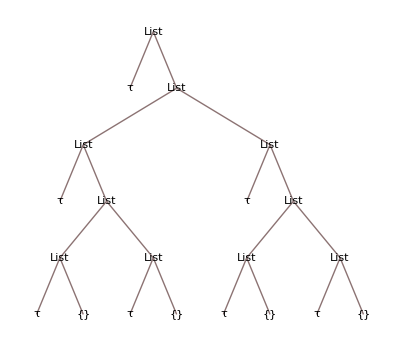

```mathematica
fullstruct@3//TreeForm
```

```mathematica
α={0.5,.5}+{0,0.2}
```

{0.5,0.7}

```mathematica
α=α/Norm[α]
```

{0.581238,0.813733}

```mathematica
α.A
```

{0.290619,0.441741}

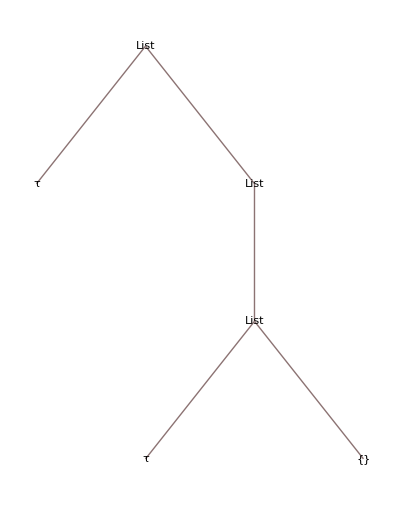

```mathematica
chain[2]//TreeForm
```

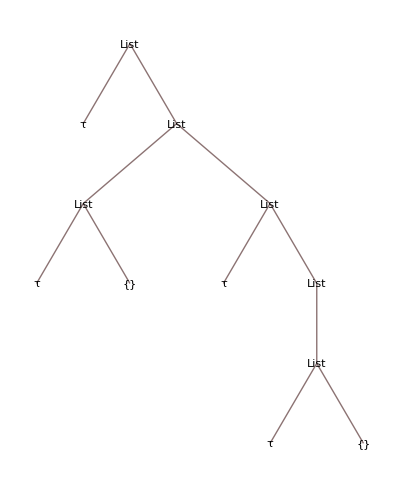

```mathematica
unbaltest=ReplacePart[fullstruct[2],{2,2}-> chain[2]];
unbaltest//TreeForm
```

```mathematica
Dimensions/@{A,α,CI12}
```

{{2,2},{2},{4,4}}

```mathematica
MatrixForm/@MCIL[A, α, CI12]@chain[2]
```

{(0.290619 | 0.441741),(1.)}

```mathematica
MatrixForm/@MCIL[A, α, CI12]@fullstruct[2]
```

{(0.290619 | 0.441741
0.290619 | 0.441741),(1.0989 | -0.32967
-0.32967 | 1.0989)}

```mathematica
GammaP[A_,α_,CI12_][ {ML1_, CIL1_}, {ML2_, CIL2_}]:=
Module[{ml12, ml1, ml2, cil1, cil2, drange,cil12,pi,DPI22,g11,g21,g22,g12,P,c12},
c12=Inverse[CI12];(*small, ok.*)
P=P12[α];
{ml1,ml2,cil1,cil2,drange}=zeroFilled[{ML1,ML2,CIL1,CIL2}];
(*Print[drange];
*)
ml12=stackdiag[ml1,ml2];
cil12=stackdiag[cil1,cil2];
DPI22=DeltaPI22[A,α,CI12][{ML1,CIL1},{ML2,CIL2}];
(*Print[MatrixForm/@{ML1,ml1,ML2,ml2,c12, ml12,c12.ml12ᵀ,DPI22}];
Print[MatrixForm/@{c12.ml12ᵀ,c12[[;;,3;;]].ml12[[{2},3;;]]ᵀ}];
Print[MatrixForm/@{c12[[;;,3;;]].ML2ᵀ}];*)
g11=Inverse[pp[Pᵀ][c12-pp[c12.ml12ᵀ][DPI22]]];
g21=-DPI22.ml12.c12.P.g11;
g12=g21ᵀ;
g22=DPI22+pp[DPI22.ml12.c12.P][g11];
ArrayFlatten@({{g11, g12[[;;,drange]]}, {g21[[drange,;;]], g22[[drange,drange]]}})
]
```

```mathematica
MatrixForm/@MCIL[A, α, CI12]@unbaltest//Chop
```

{(0.290619 | 0.441741
0.290619 | 0.441741
0.14531 | 0.23482),(1.0989 | -0.32967 | 0
-0.32967 | 1.37797 | -0.528161
0 | -0.528161 | 0.999589)}

### branch order matters!

```mathematica
unbaltest2 = ReplacePart[fullstruct[2],{2,1}-> chain[2]];unbaltest2//TreeForm;
```

```mathematica
MatrixForm/@MCIL[A, α, CI12]@unbaltest2//Chop
```

{(0.290619 | 0.441741
0.290619 | 0.441741
0.14531 | 0.23482),(1.37797 | -0.32967 | -0.528161
-0.32967 | 1.0989 | 0
-0.528161 | 0 | 0.999589)}

```mathematica
MatrixForm/@MCIL[A, α, CI12]@fullstruct[4]//Chop
```

{(0.290619 | 0.441741
0.290619 | 0.441741
0.14531 | 0.23482
0.14531 | 0.23482
0.0726548 | 0.12299
0.0726548 | 0.12299
0.0726548 | 0.12299
0.0726548 | 0.12299
0.14531 | 0.23482
0.14531 | 0.23482
0.0726548 | 0.12299
0.0726548 | 0.12299
0.0726548 | 0.12299
0.0726548 | 0.12299),(1.52819 | -0.329751 | -0.409249 | -0.409249 | 0.00289497 | 0.00289497 | 0.00289497 | 0.00289497 | 0.0000465182 | 0.0000465182 | 0.0000284278 | 0.0000284278 | 0.0000284278 | 0.0000284278
-0.329751 | 1.52819 | 0.0000465182 | 0.0000465182 | 0.0000284278 | 0.0000284278 | 0.0000284278 | 0.0000284278 | -0.409249 | -0.409249 | 0.00289497 | 0.00289497 | 0.00289497 | 0.00289497
-0.409249 | 0.0000465182 | 1.52805 | -0.329841 | -0.406243 | -0.406243 | 0.0000221755 | 0.0000221755 | -0.0000268845 | -0.0000268845 | -0.0000164294 | -0.0000164294 | -0.0000164294 | -0.0000164294
-0.409249 | 0.0000465182 | -0.329841 | 1.52805 | 0.0000221755 | 0.0000221755 | -0.406243 | -0.406243 | -0.0000268845 | -0.0000268845 | -0.0000164294 | -0.0000164294 | -0.0000164294 | -0.0000164294
0.00289497 | 0.0000284278 | -0.406243 | 0.0000221755 | 1.09862 | -0.329947 | -0.000106338 | -0.000106338 | -0.0000164294 | -0.0000164294 | -0.0000100402 | -0.0000100402 | -0.0000100402 | -0.0000100402
0.00289497 | 0.0000284278 | -0.406243 | 0.0000221755 | -0.329947 | 1.09862 | -0.000106338 | -0.000106338 | -0.0000164294 | -0.0000164294 | -0.0000100402 | -0.0000100402 | -0.0000100402 | -0.0000100402
0.00289497 | 0.0000284278 | 0.0000221755 | -0.406243 | -0.000106338 | -0.000106338 | 1.09862 | -0.329947 | -0.0000164294 | -0.0000164294 | -0.0000100402 | -0.0000100402 | -0.0000100402 | -0.0000100402
0.00289497 | 0.0000284278 | 0.0000221755 | -0.406243 | -0.000106338 | -0.000106338 | -0.329947 | 1.09862 | -0.0000164294 | -0.0000164294 | -0.0000100402 | -0.0000100402 | -0.0000100402 | -0.0000100402
0.0000465182 | -0.409249 | -0.0000268845 | -0.0000268845 | -0.0000164294 | -0.0000164294 | -0.0000164294 | -0.0000164294 | 1.52805 | -0.329841 | -0.406243 | -0.406243 | 0.0000221755 | 0.0000221755
0.0000465182 | -0.409249 | -0.0000268845 | -0.0000268845 | -0.0000164294 | -0.0000164294 | -0.0000164294 | -0.0000164294 | -0.329841 | 1.52805 | 0.0000221755 | 0.0000221755 | -0.406243 | -0.406243
0.0000284278 | 0.00289497 | -0.0000164294 | -0.0000164294 | -0.0000100402 | -0.0000100402 | -0.0000100402 | -0.0000100402 | -0.406243 | 0.0000221755 | 1.09862 | -0.329947 | -0.000106338 | -0.000106338
0.0000284278 | 0.00289497 | -0.0000164294 | -0.0000164294 | -0.0000100402 | -0.0000100402 | -0.0000100402 | -0.0000100402 | -0.406243 | 0.0000221755 | -0.329947 | 1.09862 | -0.000106338 | -0.000106338
0.0000284278 | 0.00289497 | -0.0000164294 | -0.0000164294 | -0.0000100402 | -0.0000100402 | -0.0000100402 | -0.0000100402 | 0.0000221755 | -0.406243 | -0.000106338 | -0.000106338 | 1.09862 | -0.329947
0.0000284278 | 0.00289497 | -0.0000164294 | -0.0000164294 | -0.0000100402 | -0.0000100402 | -0.0000100402 | -0.0000100402 | 0.0000221755 | -0.406243 | -0.000106338 | -0.000106338 | -0.329947 | 1.09862)}

```mathematica
CI12//MatrixForm
```

(1.0989 | 0. | -0.32967 | 0.
0. | 1.0989 | 0. | -0.32967
-0.32967 | 0. | 1.0989 | 0.
0. | -0.32967 | 0. | 1.0989)

#### get zeroes in the stiffness structure if and only if α is left eigenvector of A.

```mathematica
onebranch = {1,3,5}
```

{1,3,5}

```mathematica
aa=Inverse[MCIL[A,α,CI12][fullstruct[4]][[2]]][[onebranch, onebranch]];aa //MatrixForm
```

(1. | 0.528378 | 0.275541
0.528378 | 1.27959 | 0.674338
0.275541 | 0.674338 | 1.35585)

```mathematica
α.A
```

{0.290619,0.441741}

```mathematica
MatrixForm/@MCIL[A,α,CI12]@chain[4]
```

{(0.290619 | 0.441741
0.14531 | 0.23482
0.0726548 | 0.12299),(1.27908 | -0.530129 | 0.00372208
-0.530129 | 1.2788 | -0.528284
0.00372208 | -0.528284 | 0.999533)}

```mathematica
bb=%[[2,1]]//Inverse;bb//MatrixForm
```

(1. | 0.528378 | 0.275541
0.528378 | 1.27959 | 0.674338
0.275541 | 0.674338 | 1.35585)

```mathematica
aa/bb//MatrixForm
```

(1. | 1. | 1.
1. | 1. | 1.
1. | 1. | 1.)

#### the same!!

## Check for transformations that leave the parameters invariant

```mathematica
A
```

{{0.5,0.2},{0,0.4}}

```mathematica
α
```

{0.581238,0.813733}

```mathematica
Q1[α_]:=Orthogonalize[Join[P1[α]ᵀ,{{0,1}}] ][[{2}]]ᵀ
```

```mathematica
Q12[α_]:=KroneckerProduct[IdentityMatrix@2,Q1[α]]
```

```mathematica
Q12[{23.,22}]//MatrixForm
```

(-0.691223 | 0.
0.722642 | 0.
0. | -0.691223
0. | 0.722642)

```mathematica
P1[α]ᵀ.Q1[α]
```

{{0.}}

```mathematica
P12[α]ᵀ.Q12[α]
```

{{0.,0.},{0.,0.}}

```mathematica
MatrixForm/@{A,α,CI12}
```

{(0.5 | 0.2
0 | 0.4),(0.581238
0.813733),(1.0989 | 0. | -0.32967 | 0.
0. | 1.0989 | 0. | -0.32967
-0.32967 | 0. | 1.0989 | 0.
0. | -0.32967 | 0. | 1.0989)}

```mathematica
Q1[α]//MatrixForm
```

(-0.813733
0.581238)

```mathematica
Q12[α]//MatrixForm
```

(-0.813733 | 0.
0.581238 | 0.
0. | -0.813733
0. | 0.581238)

```mathematica
P12[α]ᵀ//MatrixForm
```

(0.581238 | 0.813733 | 0 | 0
0 | 0 | 0.581238 | 0.813733)

```mathematica
Q12[α].({{.1}, {.3}})
```

{{-0.0813733},{0.0581238},{-0.24412},{0.174371}}

```mathematica
Ap = A + Q1[α].{{0.1,.2}}
```

{{0.418627,0.0372533},{0.0581238,0.516248}}

```mathematica
Ap=A+Q1[α].{{0.1}}.Q1[α]ᵀ
```

{{0.566216,0.152703},{-0.0472973,0.433784}}

### try it

```mathematica
MatrixForm/@MCIL[A,α,CI12][fullstruct[4]]
```

{(0.290619 | 0.441741
0.290619 | 0.441741
0.14531 | 0.23482
0.14531 | 0.23482
0.0726548 | 0.12299
0.0726548 | 0.12299
0.0726548 | 0.12299
0.0726548 | 0.12299
0.14531 | 0.23482
0.14531 | 0.23482
0.0726548 | 0.12299
0.0726548 | 0.12299
0.0726548 | 0.12299
0.0726548 | 0.12299),(1.52819 | -0.329751 | -0.409249 | -0.409249 | 0.00289497 | 0.00289497 | 0.00289497 | 0.00289497 | 0.0000465182 | 0.0000465182 | 0.0000284278 | 0.0000284278 | 0.0000284278 | 0.0000284278
-0.329751 | 1.52819 | 0.0000465182 | 0.0000465182 | 0.0000284278 | 0.0000284278 | 0.0000284278 | 0.0000284278 | -0.409249 | -0.409249 | 0.00289497 | 0.00289497 | 0.00289497 | 0.00289497
-0.409249 | 0.0000465182 | 1.52805 | -0.329841 | -0.406243 | -0.406243 | 0.0000221755 | 0.0000221755 | -0.0000268845 | -0.0000268845 | -0.0000164294 | -0.0000164294 | -0.0000164294 | -0.0000164294
-0.409249 | 0.0000465182 | -0.329841 | 1.52805 | 0.0000221755 | 0.0000221755 | -0.406243 | -0.406243 | -0.0000268845 | -0.0000268845 | -0.0000164294 | -0.0000164294 | -0.0000164294 | -0.0000164294
0.00289497 | 0.0000284278 | -0.406243 | 0.0000221755 | 1.09862 | -0.329947 | -0.000106338 | -0.000106338 | -0.0000164294 | -0.0000164294 | -0.0000100402 | -0.0000100402 | -0.0000100402 | -0.0000100402
0.00289497 | 0.0000284278 | -0.406243 | 0.0000221755 | -0.329947 | 1.09862 | -0.000106338 | -0.000106338 | -0.0000164294 | -0.0000164294 | -0.0000100402 | -0.0000100402 | -0.0000100402 | -0.0000100402
0.00289497 | 0.0000284278 | 0.0000221755 | -0.406243 | -0.000106338 | -0.000106338 | 1.09862 | -0.329947 | -0.0000164294 | -0.0000164294 | -0.0000100402 | -0.0000100402 | -0.0000100402 | -0.0000100402
0.00289497 | 0.0000284278 | 0.0000221755 | -0.406243 | -0.000106338 | -0.000106338 | -0.329947 | 1.09862 | -0.0000164294 | -0.0000164294 | -0.0000100402 | -0.0000100402 | -0.0000100402 | -0.0000100402
0.0000465182 | -0.409249 | -0.0000268845 | -0.0000268845 | -0.0000164294 | -0.0000164294 | -0.0000164294 | -0.0000164294 | 1.52805 | -0.329841 | -0.406243 | -0.406243 | 0.0000221755 | 0.0000221755
0.0000465182 | -0.409249 | -0.0000268845 | -0.0000268845 | -0.0000164294 | -0.0000164294 | -0.0000164294 | -0.0000164294 | -0.329841 | 1.52805 | 0.0000221755 | 0.0000221755 | -0.406243 | -0.406243
0.0000284278 | 0.00289497 | -0.0000164294 | -0.0000164294 | -0.0000100402 | -0.0000100402 | -0.0000100402 | -0.0000100402 | -0.406243 | 0.0000221755 | 1.09862 | -0.329947 | -0.000106338 | -0.000106338
0.0000284278 | 0.00289497 | -0.0000164294 | -0.0000164294 | -0.0000100402 | -0.0000100402 | -0.0000100402 | -0.0000100402 | -0.406243 | 0.0000221755 | -0.329947 | 1.09862 | -0.000106338 | -0.000106338
0.0000284278 | 0.00289497 | -0.0000164294 | -0.0000164294 | -0.0000100402 | -0.0000100402 | -0.0000100402 | -0.0000100402 | 0.0000221755 | -0.406243 | -0.000106338 | -0.000106338 | 1.09862 | -0.329947
0.0000284278 | 0.00289497 | -0.0000164294 | -0.0000164294 | -0.0000100402 | -0.0000100402 | -0.0000100402 | -0.0000100402 | 0.0000221755 | -0.406243 | -0.000106338 | -0.000106338 | -0.329947 | 1.09862)}

```mathematica
MatrixForm/@MCIL[Ap,α,CI12][fullstruct[4]]
```

{(0.290619 | 0.441741
0.290619 | 0.441741
0.14366 | 0.235998
0.14366 | 0.235998
0.0701806 | 0.12431
0.0701806 | 0.12431
0.0701806 | 0.12431
0.0701806 | 0.12431
0.14366 | 0.235998
0.14366 | 0.235998
0.0701806 | 0.12431
0.0701806 | 0.12431
0.0701806 | 0.12431
0.0701806 | 0.12431),(1.52819 | -0.329751 | -0.409276 | -0.409276 | 0.0029203 | 0.0029203 | 0.0029203 | 0.0029203 | 0.000038373 | 0.000038373 | 0.0000360198 | 0.0000360198 | 0.0000360198 | 0.0000360198
-0.329751 | 1.52819 | 0.000038373 | 0.000038373 | 0.0000360198 | 0.0000360198 | 0.0000360198 | 0.0000360198 | -0.409276 | -0.409276 | 0.0029203 | 0.0029203 | 0.0029203 | 0.0029203
-0.409276 | 0.000038373 | 1.52808 | -0.329813 | -0.406246 | -0.406246 | 0.0000195213 | 0.0000195213 | -0.0000183486 | -0.0000183486 | -0.0000172234 | -0.0000172234 | -0.0000172234 | -0.0000172234
-0.409276 | 0.000038373 | -0.329813 | 1.52808 | 0.0000195213 | 0.0000195213 | -0.406246 | -0.406246 | -0.0000183486 | -0.0000183486 | -0.0000172234 | -0.0000172234 | -0.0000172234 | -0.0000172234
0.0029203 | 0.0000360198 | -0.406246 | 0.0000195213 | 1.0986 | -0.329967 | -0.000126781 | -0.000126781 | -0.0000172234 | -0.0000172234 | -0.0000161672 | -0.0000161672 | -0.0000161672 | -0.0000161672
0.0029203 | 0.0000360198 | -0.406246 | 0.0000195213 | -0.329967 | 1.0986 | -0.000126781 | -0.000126781 | -0.0000172234 | -0.0000172234 | -0.0000161672 | -0.0000161672 | -0.0000161672 | -0.0000161672
0.0029203 | 0.0000360198 | 0.0000195213 | -0.406246 | -0.000126781 | -0.000126781 | 1.0986 | -0.329967 | -0.0000172234 | -0.0000172234 | -0.0000161672 | -0.0000161672 | -0.0000161672 | -0.0000161672
0.0029203 | 0.0000360198 | 0.0000195213 | -0.406246 | -0.000126781 | -0.000126781 | -0.329967 | 1.0986 | -0.0000172234 | -0.0000172234 | -0.0000161672 | -0.0000161672 | -0.0000161672 | -0.0000161672
0.000038373 | -0.409276 | -0.0000183486 | -0.0000183486 | -0.0000172234 | -0.0000172234 | -0.0000172234 | -0.0000172234 | 1.52808 | -0.329813 | -0.406246 | -0.406246 | 0.0000195213 | 0.0000195213
0.000038373 | -0.409276 | -0.0000183486 | -0.0000183486 | -0.0000172234 | -0.0000172234 | -0.0000172234 | -0.0000172234 | -0.329813 | 1.52808 | 0.0000195213 | 0.0000195213 | -0.406246 | -0.406246
0.0000360198 | 0.0029203 | -0.0000172234 | -0.0000172234 | -0.0000161672 | -0.0000161672 | -0.0000161672 | -0.0000161672 | -0.406246 | 0.0000195213 | 1.0986 | -0.329967 | -0.000126781 | -0.000126781
0.0000360198 | 0.0029203 | -0.0000172234 | -0.0000172234 | -0.0000161672 | -0.0000161672 | -0.0000161672 | -0.0000161672 | -0.406246 | 0.0000195213 | -0.329967 | 1.0986 | -0.000126781 | -0.000126781
0.0000360198 | 0.0029203 | -0.0000172234 | -0.0000172234 | -0.0000161672 | -0.0000161672 | -0.0000161672 | -0.0000161672 | 0.0000195213 | -0.406246 | -0.000126781 | -0.000126781 | 1.0986 | -0.329967
0.0000360198 | 0.0029203 | -0.0000172234 | -0.0000172234 | -0.0000161672 | -0.0000161672 | -0.0000161672 | -0.0000161672 | 0.0000195213 | -0.406246 | -0.000126781 | -0.000126781 | -0.329967 | 1.0986)}

```mathematica
MCIL[Ap,α,CI12][fullstruct[3]][[2]]//Inverse//MatrixForm
```

(1. | 0.3 | 0.528378 | 0.528378 | 0.158514 | 0.158514
0.3 | 1. | 0.158514 | 0.158514 | 0.528378 | 0.528378
0.528378 | 0.158514 | 1.27959 | 0.579595 | 0.0838784 | 0.0838784
0.528378 | 0.158514 | 0.579595 | 1.27959 | 0.0838784 | 0.0838784
0.158514 | 0.528378 | 0.0838784 | 0.0838784 | 1.27959 | 0.579595
0.158514 | 0.528378 | 0.0838784 | 0.0838784 | 0.579595 | 1.27959)

### Insight: rows of ML are αᵀ A^k,k=1,2,... . Is that right?

```mathematica
α.#&/@{A,A.A,A.A.A}
```

{{0.290619,0.441741},{0.14531,0.23482},{0.0726548,0.12299}}

### yes! much easier.